## Direct Derivation of the Dynamic Regressor for a Stanford Arm examples of the theoretical results presented in: "Explicit Lagrangian Formulation of the Dynamic Regressors for Serial Manipulators", M. Gabiccini, A. Bracci, D. De Carli, M. Fredianelli, A. Bicchi submitted to the 2009 IEEE International Conference on Robotics and Automation (ICRA2009) to be held in Kobe, Japan, May 12 - 17, 2009

### Package

```mathematica
<<ScrewCalculusPro`ScrewCalculusPro`
```

### UR10e Manipulator - definition of required quantities

Denavit-Hartenberg table with joint types added in the last slot [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tableUR10e[q1_,q2_,q3_,q4_,q5_,q6_]={
{0,            -Pi/2, 0.1273,q1,"R"},
{0.6120,    0        , 0.220941,q2,"R"},
{0.5723,    0        ,-0.1719,q3,"R"},
{0,            -Pi/2, 0.1149,q4,"R"},
{0,               Pi/2 ,0.1157,q5,"R"},
{0,               0         , 0.0922,q6,"R"}
}
```

{{0,-π/2,0.1273,q1,R},{0.612,0,0.220941,q2,R},{0.5723,0,-0.1719,q3,R},{0,-π/2,0.1149,q4,R},{0,π/2,0.1157,q5,R},{0,0,0.0922,q6,R}}

```mathematica
MatrixForm[{{0,-π/2,0.1273,q1,"R"},{0.612,0,0.220941,q2,"R"},{0.5723,0,-0.1719,q3,"R"},{0,-π/2,0.1149,q4,"R"},{0,π/2,0.1157,q5,"R"},{0,0,0.0922,q6,"R"}}]
```

(0 | -π/2 | 0.1273 | q1 | R
0.612 | 0 | 0.220941 | q2 | R
0.5723 | 0 | -0.1719 | q3 | R
0 | -π/2 | 0.1149 | q4 | R
0 | π/2 | 0.1157 | q5 | R
0 | 0 | 0.0922 | q6 | R)

Symbolic variable definition [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
qsym={q1,q2,q3,q4,q5,q6}
```

{q1,q2,q3,q4,q5,q6}

List of CGi's position vectors with respect to the local D-H frames [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
CGtableUR10e=Table[ToExpression[{"a"<>ToString[i],"b"<>ToString[i],"c"<>ToString[i]}],{i,1,Length[tableUR10e@@qsym]}]
```

{{a1,b1,c1},{a2,b2,c2},{a3,b3,c3},{a4,b4,c4},{a5,b5,c5},{a6,b6,c6}}

```mathematica
CGtableUR10e ={{0,0,0},
{-0.3060,0,0},
{-0.28615,0,0},
{0,0.1719,0},
{0,-0.1149,0},
{0,0,-0.0922}}
```

{{0,0,0},{-0.306,0,0},{-0.28615,0,0},{0,0.1719,0},{0,-0.1149,0},{0,0,-0.0922}}

List of inertia matrices with respect to the local CGi's [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tensorlist=Table[ToExpression[{
{"I"<>ToString[i]<>"xx","-I"<>ToString[i]<>"xy","-I"<>ToString[i]<>"xz"},
{"-I"<>ToString[i]<>"xy","I"<>ToString[i]<>"yy","-I"<>ToString[i]<>"yz"},
{"-I"<>ToString[i]<>"xz","-I"<>ToString[i]<>"yz","I"<>ToString[i]<>"zz"}
}],{i,1,Length[tableUR10e@@qsym]}]
```

{{{I1xx,-I1xy,-I1xz},{-I1xy,I1yy,-I1yz},{-I1xz,-I1yz,I1zz}},{{I2xx,-I2xy,-I2xz},{-I2xy,I2yy,-I2yz},{-I2xz,-I2yz,I2zz}},{{I3xx,-I3xy,-I3xz},{-I3xy,I3yy,-I3yz},{-I3xz,-I3yz,I3zz}},{{I4xx,-I4xy,-I4xz},{-I4xy,I4yy,-I4yz},{-I4xz,-I4yz,I4zz}},{{I5xx,-I5xy,-I5xz},{-I5xy,I5yy,-I5yz},{-I5xz,-I5yz,I5zz}},{{I6xx,-I6xy,-I6xz},{-I6xy,I6yy,-I6yz},{-I6xz,-I6yz,I6zz}}}

```mathematica
tensorlist ={{{0.031474312576900,0,0},{0,0.021875625000000,0},{0,0,0.031474312576900}},
{{0.036365625000000,0,0},{0,1.632467283798000,0},{0,0,1.632467283798000}},
{{0.010884375000000,0,0},{0,0.427952347172000,0},{0,0,0.427952347172000}},
{{0.005108247956700,0,0},{0,0.005108247956700,0},{0,0,0.005512500000000}},
{{0.005108247956700,0,0},{0,0.005512500000000,0},{0,0,0.005108247956700}},
{{0.0005264622894150000,0,0},{0,0.0005681250000000000,0},{0,0,0.0005264622894150000}}}
```

{{{0.0314743,0,0},{0,0.0218756,0},{0,0,0.0314743}},{{0.0363656,0,0},{0,1.63247,0},{0,0,1.63247}},{{0.0108844,0,0},{0,0.427952,0},{0,0,0.427952}},{{0.00510825,0,0},{0,0.00510825,0},{0,0,0.0055125}},{{0.00510825,0,0},{0,0.0055125,0},{0,0,0.00510825}},{{0.000526462,0,0},{0,0.000568125,0},{0,0,0.000526462}}}

```mathematica
tensorlist ={{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,0}}}
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
(*tensorlist ={{{0.031474312576900,0,0},{0,0.031474312576900,0},{0,0,0.021875625000000}},
{{0.036365625000000,0,0},{0,1.632467283798000,0},{0,0,1.632467283798000}},
{{0.010884375000000,0,0},{0,0.427952347172000,0},{0,0,0.427952347172000}},
{{0.005108247956700,0,0},{0,0.005512500000000,0},{0,0,0.005108247956700}},
{{0.005108247956700,0,0},{0,0.005108247956700,0},{0,0.005512500000000,0}},
{{0.0005264622894150000,0,0},{0,0.0005681250000000000,0},{0,0,0.0005264622894150000}}}*)
```

Extract just the first...

```mathematica
tensorlist[[1]]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

List of link masses [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
masslist=Table[ToExpression["m"<>ToString[i]],{i,1,Length[tableUR10e@@qsym]}]
```

{m1,m2,m3,m4,m5,m6}

```mathematica
masslist = {7.778,12.93,3.87,1.96,1.96,0.2020}
```

{7.778,12.93,3.87,1.96,1.96,0.202}

### Time dependent variable definitions [ALL REQUIRED]

Version time dependent, configuration

```mathematica
q[t_]=Map[ToExpression[ToString[#]<>"[t]"]&,qsym]
```

{q1[t],q2[t],q3[t],q4[t],q5[t],q6[t]}

Velocity

```mathematica
qp[t_]=D[q[t],t]
```

{q1'[t],q2'[t],q3'[t],q4'[t],q5'[t],q6'[t]}

Acceleration

```mathematica
qpp[t_]=D[qp[t],t]
```

{q1''[t],q2''[t],q3''[t],q4''[t],q5''[t],q6''[t]}

Reference velocity in the Slotine-Li algorithm

```mathematica
v[t_]=Table[ToExpression["v"<>ToString[i]<>"[t]"],{i,1,Length[tableUR10e@@qsym]}]
```

{v1[t],v2[t],v3[t],v4[t],v5[t],v6[t]}

Its time derivative

```mathematica
vp[t_]=D[v[t],t]
```

{v1'[t],v2'[t],v3'[t],v4'[t],v5'[t],v6'[t]}

Gravity is defined once as

```mathematica
g0={0,0,-g}
```

{0,0,-g}

### Direct regressor calculations

```mathematica
?Regressor
```

Dynamic Regressor for the first link alone

```mathematica
Y1=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,1]//FullSimplify);Y1//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+1. v1'[t] | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Y1//Dimensions
```

Dynamic Regressor for the second link alone

```mathematica
Y2=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,2]//FullSimplify);Y2//Simplify//MatrixForm
```

((-1.38778×10^-17 Sin[2 q1[t]] Sin[q2[t]]-0.187272 Sin[2 q2[t]]) v1[t] q2'[t]+v2[t] ((-1.38778×10^-17 Sin[2 q1[t]] Sin[q2[t]]-0.187272 Sin[2 q2[t]]) q1'[t]+0.135216 Cos[q2[t]] q2'[t])+(0.236087+0.187272 Cos[2 q2[t]]) v1'[t]+0.135216 Sin[q2[t]] v2'[t] | -0.612 Sin[2 q2[t]] v1[t] q2'[t]+v2[t] (-0.612 Sin[2 q2[t]] q1'[t]+0.220941 Cos[q2[t]] q2'[t])+(0.612+0.612 Cos[2 q2[t]]) v1'[t]+0.220941 Sin[q2[t]] v2'[t] | -0.612 Cos[2 q2[t]] v1[t] q2'[t]+v2[t] (-0.612 Cos[2 q2[t]] q1'[t]-0.220941 Sin[q2[t]] q2'[t])-0.612 Sin[2 q2[t]] v1'[t]+0.220941 Cos[q2[t]] v2'[t] | 0.612 Cos[q2[t]] v2[t] q2'[t]+0.441882 v1'[t]+0.612 Sin[q2[t]] v2'[t] | Sin[q2[t]] (Cos[q2[t]] (1. v2[t] q1'[t]+1. v1[t] q2'[t])+1. Sin[q2[t]] v1'[t]) | Cos[2 q2[t]] (-1. v2[t] q1'[t]-1. v1[t] q2'[t])-1. Sin[2 q2[t]] v1'[t] | 1. Cos[q2[t]] v2[t] q2'[t]+1. Sin[q2[t]] v2'[t] | Cos[q2[t]] (Sin[q2[t]] (-1. v2[t] q1'[t]-1. v1[t] q2'[t])+1. Cos[q2[t]] v1'[t]) | -1. Sin[q2[t]] v2[t] q2'[t]+1. Cos[q2[t]] v2'[t] | 0.
-0.612 g Cos[q2[t]]+0.187272 Sin[2 q2[t]] v1[t] q1'[t]+0.135216 Sin[q2[t]] v1'[t]+0.374544 v2'[t] | -1. g Cos[q2[t]]+Sin[2 q2[t]] (0.612 v1[t] q1'[t]-2.77556×10^-17 v2[t] q2'[t])+0.220941 Sin[q2[t]] v1'[t]+1.224 v2'[t] | 1. g Sin[q2[t]]+Cos[2 q2[t]] (0.612 v1[t] q1'[t]-5.55112×10^-17 v2[t] q2'[t])+0.220941 Cos[q2[t]] v1'[t] | -1.38778×10^-17 Cos[q2[t]] v2[t] q1'[t]+0.612 Sin[q2[t]] v1'[t] | -0.5 Sin[2 q2[t]] v1[t] q1'[t] | 1. Cos[2 q2[t]] v1[t] q1'[t] | 1. Sin[q2[t]] v1'[t] | 0.5 Sin[2 q2[t]] v1[t] q1'[t] | 1. Cos[q2[t]] v1'[t] | 1. v2'[t]
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Regressor for the whole manipulator

```mathematica
Y=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0]);
```

```mathematica
Y//Dimensions
```

{6,60}

Structure of the Regressor for the Stanford Manipulator - the white columns show which parameters do not affect the manipulator dynamics

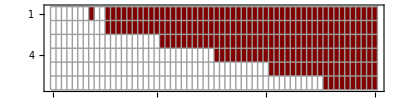

```mathematica
MatrixPlot[Y,ColorFunction->"Monochrome",AspectRatio->(1/4),Mesh-> All]
```

```mathematica
theFile=File["Yyyyy.txt"];
Export[theFile,Y//Chop];
```

### Standard way of deriving the equations of motion

Calculation of all 6 equations of motion

```mathematica
classicaleqs=DynamicEquations[tableUR10e@@q[t],CGtableUR10e,masslist,tensorlist,g0,q[t],qp[t],v[t],vp[t]];
```

We show just the first one...

```mathematica
classicaleqs[[1]];
```

### Equations of motion obtained multiplying the Dynamic Regressor and the List of Dynamic Parameters

Contestualmente alla creazione della lista di parametri (10 per ciascun link) i momenti di inerzia vengono scritti rispetto all'origine del frame di DH ancora in componenti nel frame di DH.

As we create the complete list with masses, first moments of inertia and second moments of inertia, we calculate the moments of inertia with respect to the local D-H frames, as indicated in the paper

```mathematica
paramlist=ExtractParameters[CGtableUR10e,masslist,tensorlist]//Simplify;paramlist
```

{7.778,0.,0.,0.,0.0314743,0.,0.,0.0218756,0.,0.0314743,12.93,-3.95658,0.,0.,0.0363656,0.,0.,2.84318,0.,2.84318,3.87,-1.1074,0.,0.,0.0108844,0.,0.,0.744835,0.,0.744835,1.96,0.,0.336924,0.,0.0630255,0.,0.,0.00510825,0.,0.0634297,1.96,0.,-0.225204,0.,0.0309842,0.,0.,0.0055125,0.,0.0309842,0.202,0.,0.,-0.0186244,0.00224363,0.,0.,0.00228529,0.,0.000526462}

Extract just the parameters for the first link...

```mathematica
paramlist[[1;;10]]
```

{m1,0,0,0,0,0,0,0,0,0}

Equations of motion with the regressor

```mathematica
regressoreqs=Y.paramlist;
```

### A little detour inside the package (just to show other useful functions)

Computation of the forward kinematics for the defined Denavit-Hartenberg table

```mathematica
FK= DHFKine[tableUR10e@@qsym]//FullSimplify
FK//Dimensions
```

{{1. Cos[q6] Sin[q1] Sin[q5]+Cos[q1] (Cos[q2+q3+q4] Cos[q5] Cos[q6]-1. Sin[q2+q3+q4] Sin[q6]),-1. Sin[q1] Sin[q5] Sin[q6]+Cos[q1] (-1. Cos[q6] Sin[q2+q3+q4]-1. Cos[q2+q3+q4] Cos[q5] Sin[q6]),-1. Cos[q5] Sin[q1]+1. Cos[q1] Cos[q2+q3+q4] Sin[q5],(-0.163941-0.0922 Cos[q5]) Sin[q1]+Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]-0.0461 Sin[q2+q3+q4-q5]+0.0461 Sin[q2+q3+q4+q5])},{Cos[q2+q3+q4] Cos[q5] Cos[q6] Sin[q1]-1. Cos[q1] Cos[q6] Sin[q5]-1. Sin[q1] Sin[q2+q3+q4] Sin[q6],-1. Cos[q6] Sin[q1] Sin[q2+q3+q4]+(-1. Cos[q2+q3+q4] Cos[q5] Sin[q1]+1. Cos[q1] Sin[q5]) Sin[q6],1. Cos[q1] Cos[q5]+1. Cos[q2+q3+q4] Sin[q1] Sin[q5],Cos[q1] (0.163941+0.0922 Cos[q5])+Sin[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3]-0.1157 Sin[q2+q3+q4]-0.0461 Sin[q2+q3+q4-q5]+0.0461 Sin[q2+q3+q4+q5])},{-1. Cos[q5] Cos[q6] Sin[q2+q3+q4]+0.5 Sin[q2+q3+q4-q6]-0.5 Sin[q2+q3+q4+q6],-0.5 Cos[q2+q3+q4-q6]-0.5 Cos[q2+q3+q4+q6]+1. Cos[q5] Sin[q2+q3+q4] Sin[q6],-0.5 Cos[q2+q3+q4-q5]+0.5 Cos[q2+q3+q4+q5],0.1273-0.1157 Cos[q2+q3+q4]-0.0461 Cos[q2+q3+q4-q5]+0.0461 Cos[q2+q3+q4+q5]-0.612 Sin[q2]-0.5723 Sin[q2+q3]},{0.,0.,0.,1.}}

{4,4}

```mathematica
theFile=File["FK.txt"];
```

```mathematica
Export[theFile,FK];
```

Full Jacobian (classical for differntial kinematics)

```mathematica
JJ=DHJacob0[tableUR10e@@qsym]//FullSimplify
```

```mathematica
theFile=File["JJ.txt"];
Export[theFile,JJ];
```

```mathematica
D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify
```

Derivata del jacobiano

```mathematica
theFile=File["DJJ.txt"];
Export[theFile,D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify];
```

Set::write: Tag List in «1» is Protected.

Partial Jacobians (version for regressor dynamics) - reference points are still the origins of DH frames

For the first link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,1]//FullSimplify
```

For the second link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,2]//FullSimplify
```

Partial Jacobians (version for classical dynamics) - reference points are now the CGs of the link - a separate list must be supplied

First link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,1]
```

Third link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,3]
```

Inertia matrix

```mathematica
Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]
```

{1}
 |  |  |  |

```mathematica
theFile=File["Bbbbb.txt"];
Export[theFile,Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify];
```

We map it of the time dependent joint vector

```mathematica
Bmat@@qsym
```

We check its symmetry!

```mathematica
Bmat@@qsym
```

```mathematica
(*Bmat@@qsym-Transpose[Bmat@@qsym]//Simplify*)
```

We compute the Coriolis matrix derived from the Christoffel symbols

```mathematica
Cmat=InertiaToCoriolis[Bmat@@q[t],q[t],qp[t]];
```

```mathematica
Cmat[1]
```

```mathematica
Cmat = Simplify[Cmat,TimeConstraint->0.1]//Timing
```

```mathematica
Cmat=Cmat//Chop
```

```mathematica
Cmat = Cmat//Simplify
```

```mathematica
theFile=File["C.txt"];
Export[theFile,Cmat];
```

```mathematica
Gvec=Gravitational[tableUR10e@@qsym,CGtableUR10e,masslist,g0]//FullSimplify
```

```mathematica
theFile=File["G.txt"];
Export[theFile,Gvec];
```